```mathematica
ClearAll["Global`*"]
```

## Import spectrum computation from C++ result

Browse the Data folder to find a suitable computation

```mathematica
FileNames[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/decayspec*"]]
FileNames[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/decayspec_20250120_145127/*"]]
```

{/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/decayspec_20250120_145127}

{/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/decayspec_20250120_145127/decayspec.txt,/home/tobiasb/OneDrive/projects/MasterThesis_HeavyIonCollisions/code/C++/DCCspec/Data/decayspec_20250120_145127/primespec.txt}

...and CTRL+C/CTRL+V the corresponding pathname into the following variable. We need the primary spectrum as an interpolated function and the decay parameters (masses) to perform the computation.

# 20250120_145127
# primespec:	Data/spec_real_constfield_m140_20250116_115949/spec_20250117_150131/spectr.txt
# qmax:	2
# ma:	0.8
# mb:	0.14
# mc:	0.14
# [=>] pabc:	0.3747
# [=>] Eabc:	0.4
# B:	1
# Q:	1

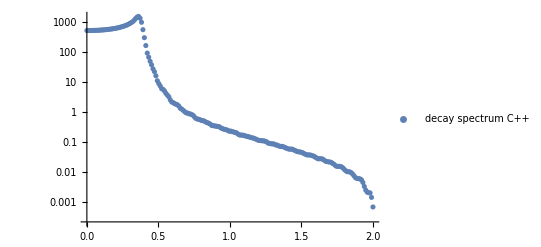

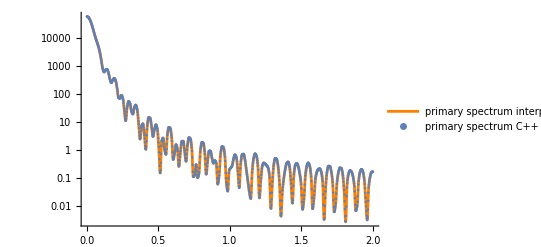

```mathematica
cppspecfolder="decayspec_20250120_145127";
datadecayspec=Import[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/"<>cppspecfolder<>"/decayspec.txt"],"CSV"];
dataprimespec=Import[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/"<>cppspecfolder<>"/primespec.txt"],"CSV"];
Print[TableForm[datadecayspec[[1;;10]]]]

pTs=Transpose[datadecayspec[[12;;]]][[1]];
qTs=Transpose[dataprimespec[[3;;]]][[1]];
qTmax=qTs[[-1]];
decayspeclist=Transpose[datadecayspec[[12;;]]][[2]];
primespeclist=Transpose[dataprimespec[[3;;]]][[2]];

primespecloglist=Log@primespeclist;
primespeclog=Interpolation[Transpose@{qTs,primespecloglist}];
primespec[q_]=Exp[primespeclog[q]];

ListLogPlot[Transpose@{pTs,decayspeclist},PlotLegends->{"decay spectrum C++"}]
Show[
LogPlot[primespec[qT],{qT,0,qTmax},PlotStyle->Orange,PlotLegends->{"primary spectrum interpolated"}],
ListLogPlot[Transpose@{qTs,primespeclist},PlotLegends->{"primary spectrum C++"}]
]
```

## Small section to derive the analytic expressions relevant for the spectrum computation

```mathematica
w[p_,m_]=√(p^2+m^2);
g[t_,u_,v_]=-u*w[t*Q,ma]*w[p,mb]+t*v*Q*p+ma*Eabc;
Print["dg/dt:",D[g[t,u,v],t]];
Print["dg/du:",D[g[t,u,v],u]];
Print["dg/dv:",D[g[t,u,v],v]];
ustar[t_,v_]=(ma*Eabc+t*v*Q*p)/(w[t*Q,ma]*w[p,mb]);
Print["du*/dt:",D[ustar[t,v]//FullSimplify,t]];
Print["Note: ((p Q v)/(√(mb^2))-Q^2/(√(mb^2)))-(ma Q ( -t Q Eabc + v ma p))/(√(mb^2)) is equal to ",(((p Q v)/(√(mb^2+p^2) √(ma^2+Q^2 t^2))-(Q^2 t (Eabc ma+p Q t v))/(√(mb^2+p^2) (ma^2+Q^2 t^2)^(3/2)))-(ma Q ( -t Q Eabc+v ma p))/(√(mb^2+p^2) (ma^2+Q^2 t^2)^(3/2)))//FullSimplify]
Print["du*/dv:",D[ustar[t,v]//FullSimplify,v]];

s=Solve[1==ustar[t,v],v];
v1[t_,p_]=v/.s[[1]]//FullSimplify;
t1min[p_]=t/.Solve[0==D[v1[t,p],t],t][[2]]//FullSimplify;
vmin[p_]=v1[t1min[p],p]//FullSimplify;
s2=Solve[1==v1[t,p],t]//FullSimplify;
tmin[p_]=t/.s2[[1]]//FullSimplify;
tmax[p_]=t/.s2[[2]]//FullSimplify;
Print["u*(t,p)==1 at v1(t,p)=",v1[t,p]]
Print["v1(t,p) has a minimum at t=",t1min[p]," and v1=",vmin[p]]
Print["v1(t,p)=+1 at tmin(p)=",tmin[p]]
Print["v1(t,p)=+1 at tmax(p)=",tmax[p]]

Clear[w,ustar,g,s,v1,t1min,vmin,s2,tmin,tmax]
```

dg/dt:-(√(mb^2+p^2) Q^2 t u)/(√(ma^2+Q^2 t^2))+p Q v

dg/du:-√(mb^2+p^2) √(ma^2+Q^2 t^2)

dg/dv:p Q t

du*/dt:(p Q v)/(√(mb^2+p^2) √(ma^2+Q^2 t^2))-(Q^2 t (Eabc ma+p Q t v))/(√(mb^2+p^2) (ma^2+Q^2 t^2)^(3/2))

Note: ((p Q v)/(√(mb^2))-Q^2/(√(mb^2)))-(ma Q ( -t Q Eabc + v ma p))/(√(mb^2)) is equal to 0

du*/dv:(p Q t)/(√(mb^2+p^2) √(ma^2+Q^2 t^2))

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

u*(t,p)==1 at v1(t,p)=(-Eabc ma+√(mb^2+p^2) √(ma^2+Q^2 t^2))/(p Q t)

v1(t,p) has a minimum at t=(√(ma^2 (-Eabc^2+mb^2+p^2)))/(Eabc Q) and v1=(Eabc (-Eabc ma+√(mb^2+p^2) √((ma^2 (mb^2+p^2))/Eabc^2)))/(p √(ma^2 (-Eabc^2+mb^2+p^2)))

v1(t,p)=+1 at tmin(p)=(Eabc ma p-√((ma^2 (Eabc-mb) (Eabc+mb) (mb^2+p^2))/Q^2) Q)/(mb^2 Q)

v1(t,p)=+1 at tmax(p)=(Eabc ma p+√((ma^2 (Eabc-mb) (Eabc+mb) (mb^2+p^2))/Q^2) Q)/(mb^2 Q)

## Perform the full decay computation in Mathematica

```mathematica
Install[StringJoin[NotebookDirectory[],"Cuba-4.2.2/Cuhre"]];
ComputeDecaySpec[ps_,ma_,mb_,mc_,B_,Q_,qmax_,primespec_]:=Module[{pabc,Eabc,w,absgradg,ustar,area,myintegrand,tlower,tupper,vlower,tmin,tmax,vmin,MyIntegral,result},
pabc=1/(2*ma)√(((ma+mb)^2-mc^2)*((ma-mb)^2-mc^2));
Eabc=√(mb^2+pabc^2);

w[p_,m_]=√(p^2+m^2);
absgradg[p_,t_,u_,v_]=√((-t*u*Q^2*w[p,mb]/w[t*Q,ma]+v*Q*p)^2+(w[p,mb]*w[t*Q,ma])^2+(t*Q*p)^2);
ustar[p_,t_,v_]=(ma*Eabc+t*v*Q*p)/(w[t*Q,ma]*w[p,mb]);
area[p_,t_,v_]=√(((ma*Q*(-t*Q*Eabc+v*ma*p))/(w[p,mb]*w[t*Q,ma]^3))^2+(-1)^2+((t*Q*p)/(w[p,mb]*w[t*Q,ma]))^2);
myintegrand[p_,t_,v_]=If[ustar[p,t,v]>1,
t*primespec[t*Q]*1/(√(ustar[p,t,v]^2-1)*√(1-v^2))*area[p,t,v]/absgradg[p,t,ustar[p,t,v],v],0];



tlower[p_]=(Eabc *ma* p-√((ma^2 *(Eabc-mb) *(Eabc+mb) *(mb^2+p^2))/Q^2)* Q)/(mb^2 *Q);
tupper[p_]=(Eabc *ma* p+√((ma^2 *(Eabc-mb) *(Eabc+mb) *(mb^2+p^2))/Q^2)* Q)/(mb^2 *Q);
vlower[p_]=(Eabc* (-Eabc *ma+√(mb^2+p^2) *√((ma^2 *(mb^2+p^2))/Eabc^2)))/(p *√(ma^2 *(-Eabc^2+mb^2+p^2)));
tmin[p_]=If[tlower[p]>0,tlower[p],0];
tmax[p_]=If[tupper[p]<qmax/Q,tupper[p],qmax/Q];
vmin[p_]=If[Eabc^2<mb^2+p^2,vlower[p],-1];

MyIntegral[p_]:=(ma*B*Q*Q)/(π*pabc)*Cuhre[myintegrand[p,t,v],{t,tmin[p],tmax[p]},{v,vmin[p],1},Verbose->0][[1]][[1]];
result=Map[MyIntegral,ps];
result
]
```

You need to copy the decay parameter from above manually for each new dataset! Let’s compute on a smaller pT-grid, since this is just a test...

```mathematica
ma=0.8;
mb=0.14;
mc=0.14;
B=1;
Q=1;

pTstest=Array[#&,50,{0.001,2}]

decayspec=ComputeDecaySpec[pTstest,ma,mb,mc,B,Q,qTmax,primespec];

Clear[ma,mb,mc,B,Q]
```

{0.001,0.0417959,0.0825918,0.123388,0.164184,0.20498,0.245776,0.286571,0.327367,0.368163,0.408959,0.449755,0.490551,0.531347,0.572143,0.612939,0.653735,0.694531,0.735327,0.776122,0.816918,0.857714,0.89851,0.939306,0.980102,1.0209,1.06169,1.10249,1.14329,1.18408,1.22488,1.26567,1.30647,1.34727,1.38806,1.42886,1.46965,1.51045,1.55124,1.59204,1.63284,1.67363,1.71443,1.75522,1.79602,1.83682,1.87761,1.91841,1.9592,2.}

Cuhre::accuracy: Desired accuracy was not reached within 50115 function evaluations on 386 subregions.

General::stop: Further output of Cuhre::accuracy will be suppressed during this calculation.

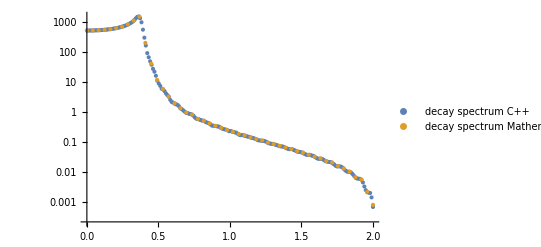

```mathematica
ListLogPlot[{Transpose@{pTs,decayspeclist},Transpose@{ps,decayspec}},PlotLegends->{"decay spectrum C++","decay spectrum Mathematica"}]
```